The Langevin function is

```mathematica
L[x_]:=Coth[x]-1/x
```

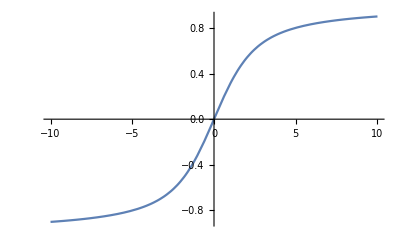

```mathematica
Plot[
L[x],{x,-10,10}
]
```

Giving M in units of M_s and parameter a in units of μ_0, we can solve the Weiss mean field equation:

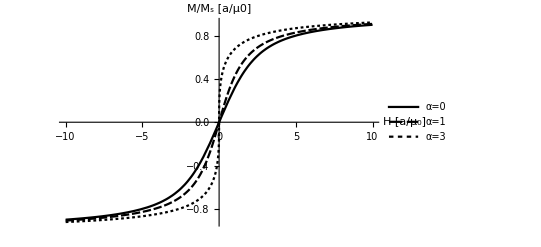

```mathematica
plot=Plot[
{
L[H/a]/.{a->1},
M/.FindRoot[(L[(H+α M)/a]/.{a->1,α->1})-M,{M,1}],
M/.FindRoot[(L[(H+α M)/a]/.{a->1,α->3})-M,{M,1}]
},
{H,-10,10},
PlotLegends->Placed[{"α=0","α=1","α=3"},Top],
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16
]
```

```mathematica
(* Export["C:\\Users\\Jakob\\Documents\\CENTREX Jakob\\0 common\\thesis\\figs\\mathematica\\weiss.pdf",plot] *)
```

#### Jiles-Atherton

Define the Langevin function:

```mathematica
L[x_]:=Coth[x]-1/x
```

Solve for the first curve (ascending in H):

```mathematica
M0[params_]:=M/.NDSolve[
{(k ( M'[H]/(1+α M'[H]))==L[(H+α M[H])/a]-M[H])/.params,(M[Hi0+dH]==Mi0)/.params},
M,{H,Hi0+dH,Hf0+dH}/.params]⟦1,1⟧;
```

Define a function that gives the next curve (changes direction of H change, and reduces the range of H):

```mathematica
Mnext[Mprev_,δ_,params_]:=M/.NDSolve[
{((-1)^δ k( M'[H]/(1+α M'[H]))==L[(H+α M[H])/a]-M[H])/.params,M[Mprev["Domain"]⟦1,Mod[δ,2]+1⟧]==Mprev[Mprev["Domain"]⟦1,Mod[δ,2]+1⟧]},
M,{H,Mprev["Domain"]⟦1,Mod[δ,2]+1⟧,(decay*(Mprev["Domain"]⟦1,Mod[δ+1,2]+1⟧-dH)+dH)/.params}
]⟦1,1⟧;
```

Define a function to plot a curve:

```mathematica
p[M_]:=Plot[
Evaluate[M[H]],
{H,M["Domain"]⟦1,1⟧,M["Domain"]⟦1,2⟧},
PlotRange->{M["Domain"]⟦1⟧,All},
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16,
PlotStyle->Thickness[0.002]
]
```

Repeat the degaussing for N times:

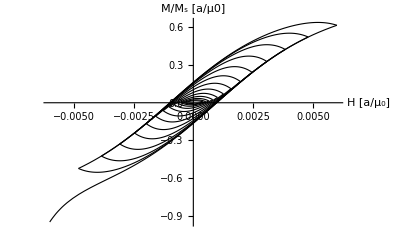

```mathematica
params={Hi0->-.006,Hf0->.006,Mi0->-.95,a->0.002,α->0.00033,k->0.001,decay->0.8};
dHpar[dH0_]:=params~Join~{dH->dH0};
p2=dHpar[0];
Ntimes=25;

Marr = NestList[
{Mnext[#⟦1⟧,#⟦2⟧+1,p2],#⟦2⟧+1,p2}&,
{M0[p2],0,p2},Ntimes];
Show[Table[p[x⟦1⟧],{x,Marr}]]
```

Find the final magnetization as a function of the offset dH:

```mathematica
dHarr=Table[x/10,{x,-50,50}];
Ntimes=25;

MMarr=Table[
NestList[{Mnext[#⟦1⟧,#⟦2⟧+1,dHpar[dH0]],#⟦2⟧+1,dHpar[dH0]}&,
{M0[dHpar[dH0]],0,dHpar[dH0]},Ntimes],
{dH0,dHarr}
];

finalM=Table[
Marr⟦-1,1⟧[Marr⟦-1,1⟧["Domain"]⟦1,1⟧],
{Marr,MMarr}];

lp=ListPlot[
Transpose[{dHarr,finalM}],
Joined->True,
PlotTheme->"Monochrome",
AxesLabel->{"ΔH [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16,
GridLines->Automatic,
PlotMarkers->None,
PlotStyle->{Red}
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.0814514+ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {H,M[H]} = {0.,-0.0814514}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.0814514+ComplexInfinity+ComplexInfinity encountered.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {H,M[H]} = {0.,-0.0814514}.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.0814513+ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NDSolve::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {H,M[H]} = {0.,-0.0814513}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

NDSolve::ndnum: Encountered non-numerical value for a derivative at H == 0..

ReplaceAll::reps: {0.5 M'[H]==-2/H+Coth[H/2]-M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (M/.0.5 M'[H]==-2/H+Coth[H/2]-M[H])[Domain]⟦1,2⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (M/.0.5 M'[H]==-2/H+Coth[H/2]-M[H])[Domain]⟦1,2⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partd: Part specification (M/.0.5 M'[H]==-2/H+Coth[H/2]-M[H])[Domain]⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {0.5 M'[H]==-2./H+Coth[0.5 H]-1. M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dvnoarg: The function M appears with no arguments.

ReplaceAll::reps: {-0.5 M'[H]==-2/H+Coth[H/2]-M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dvnoarg: The function M appears with no arguments.

General::stop: Further output of NDSolve::dvnoarg will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (M/.-0.5 M'[H]==-2/H+Coth[H/2]-M[H])[Domain]⟦1,1⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {-0.5 M'[H]==-2./H+Coth[0.5 H]-1. M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification (M/.-0.5 M'[H]==-2./H+Coth[0.5 H]-1. M[H])[Domain]⟦1,1⟧ is longer than depth of object.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: {-0.5 M'[H]==-2./H+Coth[0.5 H]-1. M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partd: Part specification (M/.-0.5 M'[H]==-2./H+Coth[0.5 H]-1. M[H])[Domain]⟦1,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Compare with the Weiss model (black dashed line):

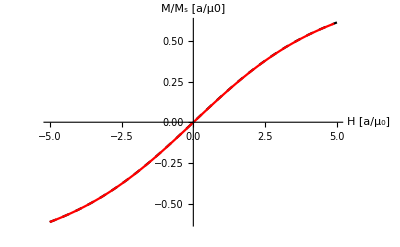

```mathematica
weiss=Plot[
M/.FindRoot[(L[(H+α M)/a]/.params)-M,{M,1}],
{H,Hi0,Hf0}/.params,
PlotTheme->"Monochrome",
AxesLabel->{"H [a/μ_0]","M/M_s [a/μ0]"},
BaseStyle->FontSize->16,
PlotStyle->{Black,Dashed}
];
Show[weiss,lp]
```

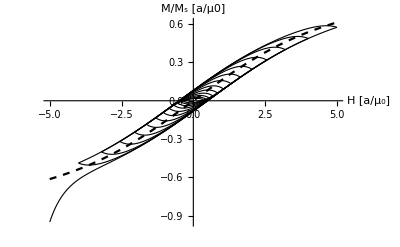

```mathematica
plot2=Show[Table[p[x⟦1⟧],{x,Marr}],weiss]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["jiles_atherton.pdf",plot2]
```

/home/jk/temp/thesis/figs/mathematica

jiles_atherton.pdf

Find the slope of the last minor loop

```mathematica
MMarr⟦15,-1,1⟧[(MMarr⟦15,-1,1⟧["Domain"]⟦1,1⟧+MMarr⟦15,-1,1⟧["Domain"]⟦1,2⟧)/2]
```

ReplaceAll::reps: {0.5 M'[H]==-2/H+Coth[H/2]-M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-0.5 M'[H]==-2/H+Coth[H/2]-M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {0.5 M'[H]==-2/H+Coth[H/2]-M[H]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-0.489743